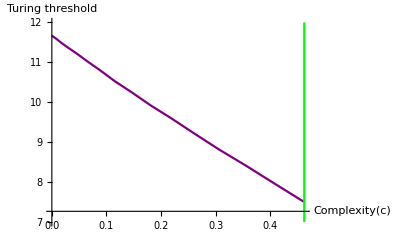

```mathematica
Clear["Global`*"];

(*Model parameters*)
(*Fraction of the community prey/predator*)
gammafracu = 1.0/2.0;
gammafracv = 1.0/2.0;
(*intra-species interaction strengths*)
du = 1.0;
dv = 1.0;
(*Mean inter-species interctions (multipled by the connectance and total number of species)*)
ncmuuu =4.0;
ncmuuv = -4.0;
ncmuvu = 4.0;
ncmuvv = -2.0;
(*Asymmetry parameters*)
gammau = 1.0;
gammav = -1.0;
gammauv = 0.0;
(*Prey species dispersal coeffcient*)
ddu = 1.0;
(*Predator species dispersal coefficient range*)
ddvmin= 7.0;
ddvmax =12.0;
numddv = 201;
ddvvec = Table[x, {x, ddvmin, ddvmax, (ddvmax - ddvmin)/(numddv-1)}];

(*Range of the complexity parameter to test*)
sqrtcompmin = 0.0;
sqrtcompmax =0.85;
numsqrtcomp= 21;
sqrtcompvec = Table[x, {x, sqrtcompmin, sqrtcompmax, (sqrtcompmax - sqrtcompmin)/(numsqrtcomp-1)}];


(*Looking for the critical ratio of disersal rates (if the well-mixed system is stable) and the critical value for the complexity*)
critdiffturing= Table[0, {x,numsqrtcomp}];
critbulk = 0;
critbulkloc = 0;
critq0 = 0;
critq0loc = 0;


flagbulk= 0;
flagq0 = 0;
k = 1;
Monitor[
While[flagbulk == 0 && flagq0 ==0 && k<numsqrtcomp+1, 
sqrtcomp=sqrtcompvec[[k]];
complexity = sqrtcomp^2;

(*First test to see if the well-mixed system is stable*)
chiu0 = 0.1;
chiv0 = 0.1;
s = FindRoot[{-(du ) mychiu + gammafracu complexity gammau mychiu^2 + gammafracv complexity gammauv mychiv mychiu ==-1,  -(dv ) mychiv  + gammafracu complexity gammauv mychiu mychiv + gammafracv complexity gammav mychiv^2  ==-1},{{mychiu, chiu0 }, {mychiv,chiv0 }}];

{chiu, chiv} ={mychiu, mychiv}  /. s ;

(*Now test if various stability criteria are satisfied*)
(* Bulk crosses imaginary axis for q = 0 -- see Eq. (S83)*)
bulkcond = gammafracu chiu^2 + gammafracv chiv^2 - 1/complexity;
If[ bulkcond>0&& flagbulk ==0, flagbulk =1; critbulk = sqrtcomp; critbulkloc = k;];

flagnonzero =0;
flagzero = 0;
(* Outlier crosses for q = 0 -- see Eq. (S89) *)
outliercond  =( gammafracu ncmuuu - 1/chiu)(gammafracv ncmuvv - 1/chiv)- gammafracu gammafracv ncmuuv ncmuvu ;
If[outliercond<0, flagq0 = 1; critq0 = sqrtcomp; critq0loc =k; ];

(*Now find the critical value of the diffusion coefficients required for Turing instability*)
flagturing =0;

j = 1;
While[flagbulk ==0 && flagq0 == 0 && flagturing==0 && j<numddv +1,
ddv= ddvvec[[j]];

(*Test if outlier crosses for q ≠ 0 -- see Eq. (S101)*)
chiu0 = 0.1;
chiv0 = 0.1;
chiuy0 = 0.1;
chivx0 = 0.1;
qminsq0 = 0.1;

s = FindRoot[{gammafracu ncmuuu mychiu1 (gammafracv ncmuvv mychiv-1)+ gammafracv ncmuvv mychiv1 (gammafracu mychiu ncmuuu -1 ) - gammafracu gammafracv ncmuuv ncmuvu (mychiu mychiv1 + mychiu1 mychiv)  == 0,-(du + myqminsq ddu ) mychiu1 - ddu mychiu+2 gammafracu complexity gammau mychiu mychiu1+ gammafracv complexity gammauv (mychiv1 mychiu + mychiv mychiu1) ==0,  -(dv + myqminsq ddv ) mychiv1  - ddv mychiv + gammafracu complexity gammauv (mychiv1 mychiu + mychiv mychiu1)+ 2 gammafracv complexity gammav mychiv mychiv1 ==0,-(du + myqminsq ddu ) mychiu + gammafracu complexity gammau mychiu^2 + gammafracv complexity gammauv mychiv mychiu ==-1,  -(dv + myqminsq ddv ) mychiv  + gammafracu complexity gammauv mychiu mychiv + gammafracv complexity gammav mychiv^2  ==-1},{{mychiu, chiu0 }, {mychiv,chiv0 },{mychiu1, chiu0 }, {mychiv1,chiv0 }, {myqminsq, qminsq0}}];


{chiu, chiv, chiu1, chiv1, qminsq} ={mychiu, mychiv, mychiu1, mychiv1, myqminsq}  /. s ;

outliercondnonzero = ( gammafracu ncmuuu - 1/chiu)(gammafracv ncmuvv - 1/chiv)- gammafracu gammafracv ncmuuv ncmuvu ;
If[flagbulk==0&&flagq0==0&& outliercondnonzero<0 && flagturing ==0,flagturing = 1; critdiffturing[[k]]=ddv; ];


j = j+1;
];
k = k+1;
];
,k];


(*Plotting the results*)
plotpointsturing = Transpose[{sqrtcompvec^2, critdiffturing}];
plotpointsbulk =If[critbulk ==0,{}, Transpose[{sqrtcompvec[[critbulkloc-1]]^2*Table[1,{numddv}], ddvvec*If[critbulk==0,0,1]}]];
plotpointsq0= If[critq0 ==0, {},Transpose[{sqrtcompvec[[critq0loc-1]]^2*Table[1,{numddv}], ddvvec*If[critq0==0,0,1]}]];


flagstartturing = 0;
deletedturing = 0;
For[k = 1, k<numddv+1, k++, 
If[flagstartturing == 0 && plotpointsturing[[k-deletedturing,2]]≠ 0, flagstartturing = 1;];
If[flagstartturing == 1 && plotpointsturing[[k-deletedturing,2]]==0, plotpointsturing=Delete[plotpointsturing,k-deletedturing];deletedturing= deletedturing +1;];
];

pltturing = ListLinePlot[plotpointsturing, PlotStyle ->Purple];
pltbulk = ListLinePlot[plotpointsbulk, PlotStyle ->Green];
pltq0 = ListLinePlot[plotpointsq0, PlotStyle ->Red];

pltbulk = 
Show[ pltturing,pltbulk, pltq0, PlotRange->All, AxesLabel-> {ToExpression["\\mathrm{Complexity}(c)",TeXForm,HoldForm],ToExpression["\\mathrm{Turing threshold}",TeXForm,HoldForm]}]
(*SetDirectory[NotebookDirectory[]];
(*Export["bulk.csv",critdiffbulk]
Export["q0.csv",critdiffaq0]*)
Export["turingdiffsqrtcomp2.csv",critdiffturing]
Export["bulkinstabilitylocation.csv",critbulk]
Export["bulkinstabilitylocationloc.csv",critbulkloc]*)
```